```mathematica
CacheCycle[n_]:=CacheCycle[n]=With[
{P=Chromial[n]},
Problem[CoefficientList[P,x],CycleBaseCoeff[P]]
]
```

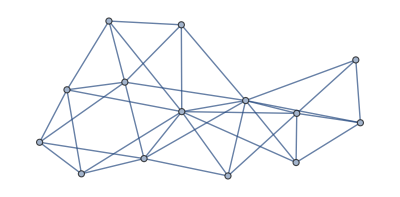

```mathematica
ReadGrof[65500]
```

```mathematica
Chromial[65500]
```

-558414 x+2744685 x^2-6110235 x^3+8196930 x^4-7419951 x^5+4799916 x^6-2288413 x^7+815833 x^8-217883 x^9+43122 x^10-6156 x^11+601 x^12-36 x^13+x^14

```mathematica
Det[Matt[3]]==1
```

-x1m3 x2m2 x3m1+x1m2 x2m3 x3m1+x1m3 x2m1 x3m2-x1m1 x2m3 x3m2-x1m2 x2m1 x3m3+x1m1 x2m2 x3m3==1

```mathematica
boega=With[{size=15},

Flatten[
Matt[size]/.Solve[
x3m2==2&&
x2m1==1&&
SkewConst[size]&&
DiagConstr[size]&&
Fold[And,
With[
{aaa=DeleteDuplicates[
Monitor[
Table[
CacheCycle[k],{k,1,19600(*58716*)}]
,k]
]},
Print[Length[aaa]];aaa
]
]
,
Vars[size]
],1]
];MatrixForm[boega]
```

326

Solve::svars: Equations may not give solutions for all "solve" variables.

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
x3m1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2+3 x3m1 | 4 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-6+7 x3m1 | 8 | 6 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-14+15 x3m1 | 16 | 10 | 10 | 5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-30+31 x3m1 | 32 | 15 | 20 | 15 | 6 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-62+63 x3m1 | 64 | 21 | 35 | 35 | 21 | 7 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-126+127 x3m1 | 128 | 28 | 56 | 70 | 56 | 28 | 8 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-254+255 x3m1 | 256 | 36 | 84 | 126 | 126 | 84 | 36 | 9 | 1 | 0 | 0 | 0 | 0 | 0
-510+511 x3m1 | 512 | 45 | 120 | 210 | 252 | 210 | 120 | 45 | 10 | 1 | 0 | 0 | 0 | 0
-1022+1023 x3m1 | 1024 | 55 | 165 | 330 | 462 | 462 | 330 | 165 | 55 | 11 | 1 | 0 | 0 | 0
-2046+2047 x3m1 | 2048 | 66 | 220 | 495 | 792 | 924 | 792 | 495 | 220 | 66 | 12 | 1 | 0 | 0
-4094+4095 x3m1 | 4096 | 78 | 286 | 715 | 1287 | 1716 | 1716 | 1287 | 715 | 286 | 78 | 13 | 1 | 0
x15m1 | x15m2 | x15m3 | x15m4 | x15m5 | x15m6 | x15m7 | x15m8 | x15m9 | x15m10 | x15m11 | x15m12 | x15m13 | x15m14 | 1)

```mathematica
Det[boega2]
```

1/73786976294838206464(-x14m1-52667 x14m10-196560 x14m11-733589 x14m12-2737801 x14m13+3739875 x14m14+x14m2-17 x14m4-73 x14m5-269 x14m6-1008 x14m7-3779 x14m8-14113 x14m9+35112 x14m10 x3m1+131042 x14m11 x3m1+489060 x14m12 x3m1+1825200 x14m13 x3m1-2493258 x14m14 x3m1+2 x14m3 x3m1+12 x14m4 x3m1+48 x14m5 x3m1+180 x14m6 x3m1+674 x14m7 x3m1+2520 x14m8 x3m1+9408 x14m9 x3m1)

```mathematica
eded =Monitor[Table[Chromial[k],{k,1,300000}],k];Length[eded]
```

```mathematica
Table[Length[Tally[
Monitor[
Table[
Chromial[k],{k,StartMpg[[size]],EndMPG[[size]](*58716*)}]
,k]
]],{size,1,9}]
```

{2,2,3,5,10,20,43,109,308}

```mathematica
byChromial=Block[{k, result,P, current},
result=Association[];
For[k=1,k≤EndMPG[[9]],k++,
P=Chromial[k];
If[!KeyExistsQ[result,P],
result[P]={k},
current = result[P];
current = Append[current, k];
result[P]=current
]
];
result
];Length[byChromial]
```

502

```mathematica
j=Association[]
```

<||>

```mathematica
j["pol"]
```

Missing[KeyAbsent,pol]

```mathematica
Total[{2,2,3,5,10,20,43,109,308}]
```

502

```mathematica
With[
{size=5},
Table[
With[
{P= CoefficientList[Chromial[k],x]},
Table[
With[
{Q= CoefficientList[Chromial[l],x]},
{Q,P}
],
{l,StartMpg[[size-1]],EndMPG[[size-1]](*58716*)}
]
],
{k,StartMpg[[size]],EndMPG[[size]](*58716*)}
]
]
```

{{{{0,-486,1539,-1998,1395,-570,137,-18,1},{0,1458,-5103,7533,-6183,3105,-981,191,-21,1}},{{0,-630,1905,-2347,1554,-605,140,-18,1},{0,1458,-5103,7533,-6183,3105,-981,191,-21,1}},{{0,-486,1539,-1998,1395,-570,137,-18,1},{0,1458,-5103,7533,-6183,3105,-981,191,-21,1}},8,{{0,-664,1992,-2432,1595,-615,141,-18,1},{0,1458,-5103,7533,-6183,3105,-981,191,-21,1}},{{0,-486,1539,-1998,1395,-570,137,-18,1},{0,1458,-5103,7533,-6183,3105,-981,191,-21,1}},{{0,-486,1539,-1998,1395,-570,137,-18,1},{0,1458,-5103,7533,-6183,3105,-981,191,-21,1}}},48,{{{0,-486,1539,-1998,1395,-570,137,-18,1},{0,1458,6,-21,1}},12,{1}}}
 |  |  |  |